```mathematica
n=30;
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
ηv[a_]:=(-1)^(a[[1]]+1);
Nv[a_]:=2(-1)^a[[1]] Cos[(π a[[1]])/4];
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(p'-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[p'], Table[{p'/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];
h = hv @@@ H;
H //Echo[#,"(r,s): "]&;
h //Echo[#,"h = "]&;
s=Outer[sv, H,H,1]//Simplify;
z={
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,2,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,1}
};
t=DiagonalMatrix[tv/@H];
```

c =   7/10

(r,s):   {{1,1},{1,2},{1,3},{1,4},{2,1},{2,2}}

h =   {0,1/10,3/5,3/2,7/16,3/80}

```mathematica
i={{{1,1},{1,1},1},{{1,1},{1,1},-1},{{1,2},{1,2},1},{{1,2},{1,2},-1},{{1,3},{1,3},1},{{1,3},{1,3},-1},{{1,4},{1,4},1},{{1,4},{1,4},-1},{{2,2},{2,2},1},{{2,2},{2,2},-1},{{2,4},{2,4},1},{{2,4},{2,4},-1},{{1,1},{1,2},0},{{1,1},{1,3},0},{{1,1},{1,4},0},{{1,1},{2,2},0},{{1,1},{2,4},0},{{1,2},{1,3},0},{{1,2},{1,4},0},{{1,2},{2,2},0},{{1,2},{2,4},0},{{1,3},{1,4},0},{{1,3},{2,2},0},{{1,3},{2,4},0},{{1,4},{2,2},0},{{1,4},{2,4},0},{{2,2},{2,4},0},{{1,1},{1,1},2},{{1,1},{1,1},-2},{{1,2},{1,2},2},{{1,2},{1,2},-2},{{1,3},{1,3},2},{{1,3},{1,3},-2},{{1,4},{1,4},2},{{1,4},{1,4},-2},{{2,2},{2,2},2},{{2,2},{2,2},-2},{{2,4},{2,4},2},{{2,4},{2,4},-2}};
ho[a_]:=(hv@@a[[1]]+hv@@a[[2]]+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:= 
(sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]+ sv[a[[1]],b[[2]]]sv[a[[2]],b[[1]]])a[[3]]b[[3]]+
sv[a[[1]],b[[1]]]sv[a[[2]],b[[1]]]a[[3]]Abs[b[[3]]]-1+
sv[a[[1]],b[[1]]]sv[a[[1]],b[[2]]]Abs[a[[3]]]-1 b[[3]]+ 
1/2 sv[a[[1]],b[[1]]]^2 Abs[a[[3]]]-1 Abs[b[[3]]]-1+
1/2 a[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-1 Abs[b[[3]]]-2+
1/2 b[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-2 Abs[b[[3]]]-1+
1/8 a[[3]]b[[3]]Total[(sv[a[[1]],#] tv[#]^2 sv[#,b[[1]]])&/@H]Exp[π ⅈ(hv@@(a[[1]]) + hv@@(b[[1]])-cv/12)]Abs[a[[3]]]-2 Abs[b[[3]]]-2;
s=Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}] // FullSimplify;

(* Here is a T matrix *)
ho[a_]:=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@(a[[1]]))/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
t=DiagonalMatrix[Exp[-2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
```

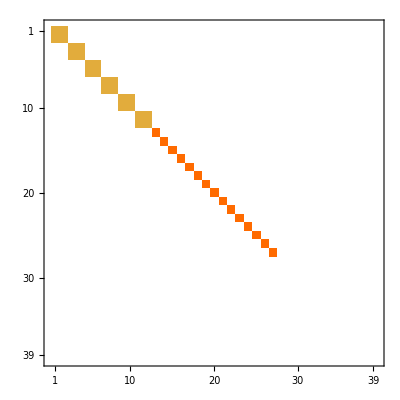

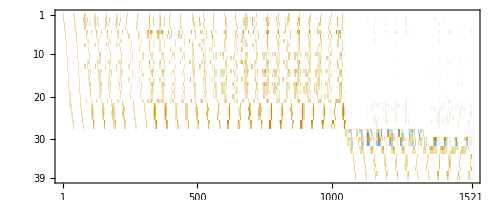

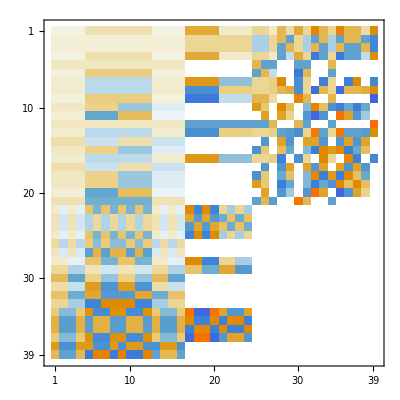

```mathematica
z//MatrixPlot
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=Conjugate[s] . ReplacePart[z,Thread[nz->X]] . s  //Flatten;
A=CoefficientArrays[Thread[m==0],X][[2]]//Simplify//Normal;
a=(A[[#,All]]&/@(Flatten[FirstPosition[#,1]&/@ RowReduce[Transpose[Chop[N[A]]]]]) )//FullSimplify;
Transpose[N[A]]//RowReduce//MatrixPlot
a//MatrixPlot
```

```mathematica
Organize[e_]:=Module[{l,r,L},
l=e[[1]];
r=e[[2]];
L=LCM@@(Level[List@@#,1]&/@Flatten[{l,r}]//Flatten//Denominator);
e[[0]][(l-r)//ExpandAll,0]
];
b=Inverse[N[a]]//Chop;
b=RootApproximant/@b;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->Simplify[b.X]]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
mx=(Min [Cases[eqn, (a_. * #)>= 0 :>a]])^-1&/@X;
m=N[ConjugateTranspose[s] . ReplacePart[z,Thread[nz->Simplify[b.(mx*X)]]] . s] ;
eqn=(# ≥ 0 & /@(m//Flatten)) //Expand//Chop//Rationalize//Expand// DeleteDuplicates;
eqn=Organize/@eqn;
eqn//MatrixForm; 
B=Table[Coefficient[eqn[[i]][[1]],X],{i,Length[eqn]}];
B//MatrixPlot;
```

```mathematica
<<math4ti2`
basis =zsolve[#>=0&/@Flatten[B.X]][[2]];
basis//MatrixForm
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
d=b. (mx*#) &/@basis //FullSimplify;
d=Sort[d,#1[[1]] <= #2[[1]]&];
d//Transpose//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(2 (5+√5))+ | √(2 (5+√5))+ | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) |  |  | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) |  | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | -2 (3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) |  | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) |  | √(3-√5) |  | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | (-3+√5)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) |  | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 |  | √(3-√5) |  | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | (-3+√5)/(√2) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 |  | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) |  | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
FindRowProducts[M_]:=Module[
{n=Length[M], results={}},
Do[
With[{product=M[[i]]*M[[j]]//Chop},
If[MemberQ[M,product],
AppendTo[results,{i,j,Position[M,product]//Flatten}]]
],{i,1,n},{j,1,n}];
results
]
FusionCandidates=FindRowProducts[d[[All,;;24]]//N//Chop];
FusionCandidates//Length
FusionCandidates//MatrixForm
```

315

(1 | 1 | {1,2}
1 | 2 | {1,2}
1 | 3 | {3}
1 | 4 | {4}
1 | 5 | {5}
1 | 6 | {6,7}
1 | 7 | {6,7}
1 | 8 | {8}
1 | 9 | {9,12}
1 | 10 | {10,11}
1 | 11 | {10,11}
1 | 12 | {9,12}
1 | 13 | {13}
1 | 14 | {14}
1 | 15 | {15}
1 | 16 | {16,17,18,19}
1 | 17 | {16,17,18,19}
1 | 18 | {16,17,18,19}
1 | 19 | {16,17,18,19}
1 | 20 | {20}
1 | 21 | {21,22}
1 | 22 | {21,22}
1 | 23 | {23}
1 | 24 | {24}
1 | 25 | {25,26}
1 | 26 | {25,26}
1 | 27 | {27}
1 | 28 | {28}
1 | 29 | {29}
1 | 30 | {30}
1 | 31 | {31}
1 | 32 | {32}
1 | 33 | {33}
1 | 34 | {34}
1 | 35 | {35}
1 | 36 | {36}
1 | 37 | {37}
1 | 38 | {38}
1 | 39 | {39}
2 | 1 | {1,2}
2 | 2 | {1,2}
2 | 3 | {3}
2 | 4 | {4}
2 | 5 | {5}
2 | 6 | {6,7}
2 | 7 | {6,7}
2 | 8 | {8}
2 | 9 | {9,12}
2 | 10 | {10,11}
2 | 11 | {10,11}
2 | 12 | {9,12}
2 | 13 | {13}
2 | 14 | {14}
2 | 15 | {15}
2 | 16 | {16,17,18,19}
2 | 17 | {16,17,18,19}
2 | 18 | {16,17,18,19}
2 | 19 | {16,17,18,19}
2 | 20 | {20}
2 | 21 | {21,22}
2 | 22 | {21,22}
2 | 23 | {23}
2 | 24 | {24}
2 | 25 | {25,26}
2 | 26 | {25,26}
2 | 27 | {27}
2 | 28 | {28}
2 | 29 | {29}
2 | 30 | {30}
2 | 31 | {31}
2 | 32 | {32}
2 | 33 | {33}
2 | 34 | {34}
2 | 35 | {35}
2 | 36 | {36}
2 | 37 | {37}
2 | 38 | {38}
2 | 39 | {39}
3 | 1 | {3}
3 | 2 | {3}
3 | 3 | {1,2}
3 | 4 | {5}
3 | 5 | {4}
3 | 6 | {6,7}
3 | 7 | {6,7}
3 | 8 | {8}
3 | 9 | {10,11}
3 | 10 | {9,12}
3 | 11 | {9,12}
3 | 12 | {10,11}
3 | 13 | {14}
3 | 14 | {13}
3 | 15 | {15}
3 | 16 | {16,17,18,19}
3 | 17 | {16,17,18,19}
3 | 18 | {16,17,18,19}
3 | 19 | {16,17,18,19}
3 | 20 | {20}
3 | 21 | {23}
3 | 22 | {23}
3 | 23 | {21,22}
3 | 24 | {24}
3 | 25 | {25,26}
3 | 26 | {25,26}
3 | 27 | {28}
3 | 28 | {27}
3 | 29 | {30}
3 | 30 | {29}
3 | 31 | {31}
3 | 32 | {32}
3 | 33 | {33}
3 | 36 | {37}
3 | 37 | {36}
3 | 38 | {38}
3 | 39 | {39}
4 | 1 | {4}
4 | 2 | {4}
4 | 3 | {5}
4 | 4 | {1,2}
4 | 5 | {3}
4 | 6 | {8}
4 | 7 | {8}
4 | 8 | {6,7}
4 | 9 | {13}
4 | 10 | {14}
4 | 11 | {14}
4 | 12 | {13}
4 | 13 | {9,12}
4 | 14 | {10,11}
4 | 32 | {33}
4 | 33 | {32}
4 | 38 | {39}
4 | 39 | {38}
5 | 1 | {5}
5 | 2 | {5}
5 | 3 | {4}
5 | 4 | {3}
5 | 5 | {1,2}
5 | 6 | {8}
5 | 7 | {8}
5 | 8 | {6,7}
5 | 9 | {14}
5 | 10 | {13}
5 | 11 | {13}
5 | 12 | {14}
5 | 13 | {10,11}
5 | 14 | {9,12}
5 | 32 | {33}
5 | 33 | {32}
5 | 38 | {39}
5 | 39 | {38}
6 | 1 | {6,7}
6 | 2 | {6,7}
6 | 3 | {6,7}
6 | 4 | {8}
6 | 5 | {8}
6 | 16 | {24}
6 | 17 | {24}
6 | 18 | {24}
6 | 19 | {24}
6 | 35 | {38}
7 | 1 | {6,7}
7 | 2 | {6,7}
7 | 3 | {6,7}
7 | 4 | {8}
7 | 5 | {8}
7 | 16 | {24}
7 | 17 | {24}
7 | 18 | {24}
7 | 19 | {24}
7 | 35 | {38}
8 | 1 | {8}
8 | 2 | {8}
8 | 3 | {8}
8 | 4 | {6,7}
8 | 5 | {6,7}
8 | 20 | {24}
8 | 35 | {39}
9 | 1 | {9,12}
9 | 2 | {9,12}
9 | 3 | {10,11}
9 | 4 | {13}
9 | 5 | {14}
9 | 15 | {24}
10 | 1 | {10,11}
10 | 2 | {10,11}
10 | 3 | {9,12}
10 | 4 | {14}
10 | 5 | {13}
10 | 15 | {24}
11 | 1 | {10,11}
11 | 2 | {10,11}
11 | 3 | {9,12}
11 | 4 | {14}
11 | 5 | {13}
11 | 15 | {24}
12 | 1 | {9,12}
12 | 2 | {9,12}
12 | 3 | {10,11}
12 | 4 | {13}
12 | 5 | {14}
12 | 15 | {24}
13 | 1 | {13}
13 | 2 | {13}
13 | 3 | {14}
13 | 4 | {9,12}
13 | 5 | {10,11}
14 | 1 | {14}
14 | 2 | {14}
14 | 3 | {13}
14 | 4 | {10,11}
14 | 5 | {9,12}
15 | 1 | {15}
15 | 2 | {15}
15 | 3 | {15}
15 | 9 | {24}
15 | 10 | {24}
15 | 11 | {24}
15 | 12 | {24}
15 | 21 | {31}
15 | 22 | {31}
15 | 23 | {31}
16 | 1 | {16,17,18,19}
16 | 2 | {16,17,18,19}
16 | 3 | {16,17,18,19}
16 | 6 | {24}
16 | 7 | {24}
17 | 1 | {16,17,18,19}
17 | 2 | {16,17,18,19}
17 | 3 | {16,17,18,19}
17 | 6 | {24}
17 | 7 | {24}
18 | 1 | {16,17,18,19}
18 | 2 | {16,17,18,19}
18 | 3 | {16,17,18,19}
18 | 6 | {24}
18 | 7 | {24}
19 | 1 | {16,17,18,19}
19 | 2 | {16,17,18,19}
19 | 3 | {16,17,18,19}
19 | 6 | {24}
19 | 7 | {24}
20 | 1 | {20}
20 | 2 | {20}
20 | 3 | {20}
20 | 8 | {24}
21 | 1 | {21,22}
21 | 2 | {21,22}
21 | 3 | {23}
21 | 15 | {31}
22 | 1 | {21,22}
22 | 2 | {21,22}
22 | 3 | {23}
22 | 15 | {31}
23 | 1 | {23}
23 | 2 | {23}
23 | 3 | {21,22}
23 | 15 | {31}
24 | 1 | {24}
24 | 2 | {24}
24 | 3 | {24}
25 | 1 | {25,26}
25 | 2 | {25,26}
25 | 3 | {25,26}
26 | 1 | {25,26}
26 | 2 | {25,26}
26 | 3 | {25,26}
27 | 1 | {27}
27 | 2 | {27}
27 | 3 | {28}
28 | 1 | {28}
28 | 2 | {28}
28 | 3 | {27}
29 | 1 | {29}
29 | 2 | {29}
29 | 3 | {30}
30 | 1 | {30}
30 | 2 | {30}
30 | 3 | {29}
31 | 1 | {31}
31 | 2 | {31}
31 | 3 | {31}
32 | 1 | {32}
32 | 2 | {32}
32 | 3 | {32}
32 | 4 | {33}
32 | 5 | {33}
33 | 1 | {33}
33 | 2 | {33}
33 | 3 | {33}
33 | 4 | {32}
33 | 5 | {32}
34 | 1 | {34}
34 | 2 | {34}
35 | 1 | {35}
35 | 2 | {35}
35 | 6 | {38}
35 | 7 | {38}
35 | 8 | {39}
36 | 1 | {36}
36 | 2 | {36}
36 | 3 | {37}
37 | 1 | {37}
37 | 2 | {37}
37 | 3 | {36}
38 | 1 | {38}
38 | 2 | {38}
38 | 3 | {38}
38 | 4 | {39}
38 | 5 | {39}
39 | 1 | {39}
39 | 2 | {39}
39 | 3 | {39}
39 | 4 | {38}
39 | 5 | {38})

```mathematica
di=Select[d,#[[1]]==1&];
dn=Select[d,#[[1]]!=1&];
Y=Array[y,{Length[d],6}];
YY=Y//Flatten;
l[i_,row_,v_:Y]:={{v[[i,1]] + I v[[i,2]],v[[i,3]] + I v[[i,4]]},{v[[i,5]] + I v[[i,6]],d[[i,24+row]]-v[[i,1]] - I v[[i,2]]}};
diff[i_,j_,k_,row_]:=Flatten[Assuming[#∈Reals&/@Flatten[Y],ComplexExpand[{Re[#],Im[#]}]]&@Flatten[l[i,row].l[j,row] - l[k,row]]];
firstPass[row_]:=Flatten[diff[#[[1]],#[[2]],#[[3,1]],row]&/@Select[FusionCandidates,Length[#[[3]]]==1&]];
```

```mathematica
res =firstPass[1];
jac=D[res,{YY}];
jacFn=Compile[{{vars,_Real, 1}},jac/.Thread[YY->vars]];
```

```mathematica
{residual, soln}=FindMinimum[
res.res,
Transpose[{YY,RandomReal[{-1,1},Length[YY]]}],
Method->{"LevenbergMarquardt"}
];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
MatrixForm/@Array[l[#,1,(Y/.soln//Chop)]&,39]
```

{(1. | 0
0 | 1.),(1. | 0
0 | 1.),(1. | 0
0 | 1.),(0.664421+0.00735399 ⅈ | -0.368428-0.664721 ⅈ
-0.345063+0.649091 ⅈ | -0.664421-0.00735399 ⅈ),(0.664421+0.00735399 ⅈ | -0.368428-0.664721 ⅈ
-0.345063+0.649091 ⅈ | -0.664421-0.00735399 ⅈ),(0.00027246-0.000495749 ⅈ | 0.000552448+0.000966264 ⅈ
-0.00105502+0.0000437715 ⅈ | -0.00027246+0.000495749 ⅈ),(0.00027246-0.000495749 ⅈ | 0.000552448+0.000966264 ⅈ
-0.00105502+0.0000437715 ⅈ | -0.00027246+0.000495749 ⅈ),(-0.00172062+0.000203447 ⅈ | 0.000858332+0.000328633 ⅈ
0.000761401-0.000522071 ⅈ | 0.00172062-0.000203447 ⅈ),(0.5 | 0
0 | 0.5),(0.5 | 0
0 | 0.5),(0.5 | 0
0 | 0.5),(0.5 | 0
0 | 0.5),(0.332211+0.00367699 ⅈ | -0.184214-0.332361 ⅈ
-0.172532+0.324546 ⅈ | -0.332211-0.00367699 ⅈ),(0.332211+0.00367699 ⅈ | -0.184214-0.332361 ⅈ
-0.172532+0.324546 ⅈ | -0.332211-0.00367699 ⅈ),(-2. | 0
0 | -2.),(-181.89-330.811 ⅈ | 743.635+31.6326 ⅈ
-351.115+612.631 ⅈ | 185.053+330.811 ⅈ),(-185.053-330.811 ⅈ | 743.635+31.6326 ⅈ
-351.115+612.631 ⅈ | 181.89+330.811 ⅈ),(-185.053-330.811 ⅈ | 743.635+31.6326 ⅈ
-351.115+612.631 ⅈ | 181.89+330.811 ⅈ),(-181.89-330.811 ⅈ | 743.635+31.6326 ⅈ
-351.115+612.631 ⅈ | 185.053+330.811 ⅈ),(446.826+52.833 ⅈ | -196.849-134.974 ⅈ
-223.894+85.7233 ⅈ | -446.826-52.833 ⅈ),(-0.918628+0.0432191 ⅈ | -0.0651705-0.0343467 ⅈ
-0.0376365-0.0498948 ⅈ | -1.08137-0.0432191 ⅈ),(-0.918628+0.0432191 ⅈ | -0.0651705-0.0343467 ⅈ
-0.0376365-0.0498948 ⅈ | -1.08137-0.0432191 ⅈ),(-0.918628+0.0432191 ⅈ | -0.0651705-0.0343467 ⅈ
-0.0376365-0.0498948 ⅈ | -1.08137-0.0432191 ⅈ),(-1. | 0
0 | -1.),(-0.849584-0.925099 ⅈ | 0.309831-0.15662 ⅈ
-0.889639+0.544152 ⅈ | 0.849584+0.925099 ⅈ),(-0.953873-0.61915 ⅈ | -0.0968808+0.420475 ⅈ
-0.685763+0.92365 ⅈ | 0.953873+0.61915 ⅈ),(0.29798-0.0517077 ⅈ | -0.273646-0.141679 ⅈ
0.0533269+0.189951 ⅈ | -0.29798+0.0517077 ⅈ),(0.29798-0.0517077 ⅈ | -0.273646-0.141679 ⅈ
0.0533269+0.189951 ⅈ | -0.29798+0.0517077 ⅈ),(0.060949+0.23963 ⅈ | 0.104273-0.237818 ⅈ
-0.238317+0.306876 ⅈ | -0.060949-0.23963 ⅈ),(0.060949+0.23963 ⅈ | 0.104273-0.237818 ⅈ
-0.238317+0.306876 ⅈ | -0.060949-0.23963 ⅈ),(1.83726-0.0864381 ⅈ | 0.130341+0.0686934 ⅈ
0.075273+0.0997896 ⅈ | 2.16274+0.0864381 ⅈ),(0 | 0
0 | 0),(0 | 0
0 | 0),(0.199014+0.169387 ⅈ | -0.189518-0.205836 ⅈ
0.383659-0.444057 ⅈ | -0.199014-0.169387 ⅈ),(0 | 0
0 | 0),(-0.267262+0.0685958 ⅈ | -0.00512385-0.000510069 ⅈ
-0.326489-0.292456 ⅈ | 0.267262-0.0685958 ⅈ),(-0.267262+0.0685958 ⅈ | -0.00512385-0.000510069 ⅈ
-0.326489-0.292456 ⅈ | 0.267262-0.0685958 ⅈ),(0 | 0
0 | 0),(0 | 0
0 | 0)}